```mathematica
Clear[z]
```

```mathematica
z=4;
```

```mathematica
n=1/2*(-(c2+c3)*ξ0+c2*ξ1-1);
m=1/2*(-(c2+c3)*ξ1+c2*ξ2);
Δ=-1/2*c3*ξ1;
δ=-1/2*c3*ξ2;
```

```mathematica
A=J/2*(z*(δ-2m)+γ*(Δ-3*n)-(c2+c3)*(z*(4n-2m-δ)+γ*(m-Δ-3n)));
B=J/2*(z*(m-δ)+γ*(n+m-Δ)+(c2+c3)*(z*(δ+m)+γ*(n+m+Δ-4δ)));
```

```mathematica
FullSimplify[A]
FullSimplify[B]
```

-1/4 J (-3 γ+c2^2 (γ (3 ξ0-4 ξ1+ξ2)-2 z (2 ξ0-3 ξ1+ξ2))+c2 (γ (3-3 ξ0+6 c3 ξ0+3 ξ1-4 c3 ξ1+c3 ξ2)-z (4+8 c3 ξ0+2 ξ1-8 c3 ξ1-2 ξ2+c3 ξ2))+c3 (γ (3+3 (-1+c3) ξ0+ξ1)+z (-4-2 ξ1+ξ2+c3 (-4 ξ0+2 ξ1+ξ2))))

1/4 J (-(1+c2+c3) γ (1+(c2+c3) ξ0)-(c2+c3) ((1+c2+c3) z+2 c3 γ) ξ1+((1+c2-c3) (c2+c3) z+(c2+c2^2+5 c2 c3+4 c3^2) γ) ξ2)

```mathematica
TraditionalForm[FullSimplify[A-B]]
```

-1/4 J (-4 γ+2 c2^2 ((γ-8) ξ0-2 (γ-5) ξ1+(γ-2) ξ2)+c2 (γ (4 (c3-1) ξ0-6 c3 ξ1+6 c3 ξ2+3 ξ1+ξ2+2)-4 (c3 (8 ξ0-6 ξ1+ξ2)+3 ξ1-3 ξ2+4))+c3 (γ (2 (c3-2) ξ0-2 c3 ξ1+4 c3 ξ2+ξ1+2)-4 (4 c3 ξ0+3 ξ1-2 ξ2+4)+4 c3 ξ1))

```mathematica
c1=Sqrt[1+d^2/J^2];
c2=1/2*(1-Sqrt[1+(d/J)^2]);
c3=1/2*(-1-Sqrt[1+(d/J)^2]);
```

```mathematica
FullSimplify[1/4 J (c2^2 (γ (8 ξ0-5 ξ1-3 ξ2)+2 z (2 ξ0+ξ1-3 ξ2))+c2 (γ (8 c3 ξ0+4 c3 ξ1-5 c3 ξ2+8)+2 z (4 c3 ξ0+c3 ξ1+2))+c3 (γ c3 (5 ξ1-4 ξ2)+4 z (c3 (ξ0+ξ2)+1)))]
```

1/(8 J)(d^2 (2 (z+γ) (4 ξ0+ξ1)-(z+6 γ) ξ2)+J^2 (γ (8-8 √(1+d^2/J^2)+(8-8 √(1+d^2/J^2)) ξ0+√(1+d^2/J^2) (10 ξ1-ξ2)-7 ξ2)-2 z (4 √(1+d^2/J^2)-4 ξ0+(-1+√(1+d^2/J^2)) ξ1+ξ2-5 √(1+d^2/J^2) ξ2)))

```mathematica
Clear[c1,c2,c3]
```

```mathematica
FullSimplify[2*N*z*J*((c2-c3)*(2*n-Δ)*(δ-m)+(c2+c3)*(2*(n^2+m^2+δ^2)-(n+Δ)*(m+δ)))]
```

1/2 (c2+c3) J N z (2+c2^2 (2 ξ0^2-7 ξ0 ξ1+7 ξ1^2+3 ξ0 ξ2-7 ξ1 ξ2+2 ξ2^2)+c2 (4 c3 ξ0^2+ξ0 (4-6 c3 ξ1)+3 ξ2+ξ1 (-7+3 c3 ξ1-c3 ξ2))+c3 (2 c3 ξ0^2+ξ1+ξ0 (4+c3 ξ1-3 c3 ξ2)+ξ2 (-3+2 c3 ξ2)))

```mathematica
FullSimplify[(c2-c3)*(2*n-Δ)*(δ-m)]
```

1/4 (c2-c3) (c2+c3) (-2-2 (c2+c3) ξ0+(2 c2+c3) ξ1) (ξ1-ξ2)

```mathematica
Plot3D[Sqrt[1+1]*Cos[x]*Cos[y]+Sin[x]*Sin[y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

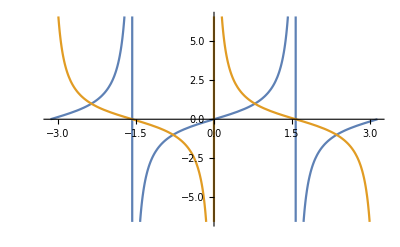

```mathematica
Plot[{Tan[x],Cot[x]},{x,-π,π}]
```

```mathematica
Tan[Pi/2]
```

ComplexInfinity

```mathematica
Cot[π/2]
```

0

```mathematica
Tan[0]*Cot[Pi/2]
```

0

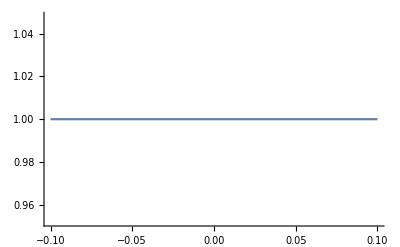

```mathematica
Plot[Cot[x]*Tan[x],{x,-0.1,0.1}]
```